```mathematica
{{0,0},{0,rl}}.Inverse[{{rr,1},{-1,ll}}].Transpose@{{0,0},{0,rl}}
```

{{0,0},{0,(rl^2 rr)/(1+ll rr)}}

```mathematica
Eigenvalues[{{0,-1},{1,0}}]
```

{ⅈ,-ⅈ}

```mathematica
f=√((2*(-(1+δ))Cos[k]+2*(1-δ))^2+4(1+δ)^2Sin[k]^2)
```

√((2 (1-δ)+2 (-1-δ) Cos[k])^2+4 (1+δ)^2 Sin[k]^2)

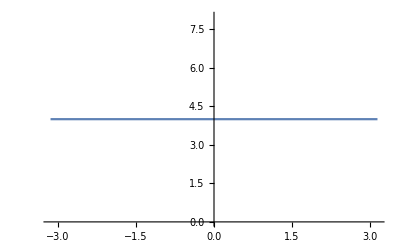

```mathematica
Plot[f/.{k->k0,δ->-1},{k0,-π,π}]
```

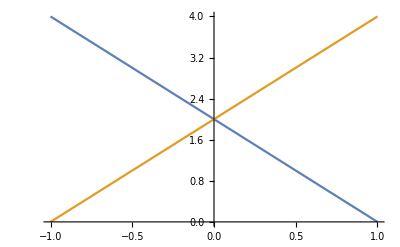

```mathematica
Plot[{Abs[2*(1-δ)],2*Abs[-(1+δ)]},{δ,-1,1}]
```

```mathematica
Inverse@{{1,1},{I,-I}}//MatrixForm
```

(1/2 | -ⅈ/2
1/2 | ⅈ/2)

```mathematica
{{1,0},{0,0}}.{0,1}
```

{0,0}

```mathematica
MatrixLog[DiagonalMatrix[{Exp[-I*π/4],Exp[I*π/4]}]]/(π/4)*I+IdentityMatrix[2]
```

{{2,0},{0,0}}

```mathematica
z1={{1},{I}}.ConjugateTranspose@{{1},{I}}/2
```

{{1/2,-ⅈ/2},{ⅈ/2,1/2}}

```mathematica
z0={{1},{-I}}.ConjugateTranspose@{{1},{-I}}/2
```

{{1/2,ⅈ/2},{-ⅈ/2,1/2}}

```mathematica
KroneckerProduct[z1,z0]//MatrixForm
```

(1/4 | ⅈ/4 | -ⅈ/4 | 1/4
-ⅈ/4 | 1/4 | -1/4 | -ⅈ/4
ⅈ/4 | -1/4 | 1/4 | ⅈ/4
1/4 | ⅈ/4 | -ⅈ/4 | 1/4)

```mathematica
z1.z1
```

{{1/2,-ⅈ/2},{ⅈ/2,1/2}}

```mathematica
p1=ArrayFlatten[{{{{0,1},{-1,0}},0*IdentityMatrix[2]},{0*IdentityMatrix[2],{{0,-1},{1,0}}}}]
```

{{0,1,0,0},{-1,0,0,0},{0,0,0,-1},{0,0,1,0}}

```mathematica
p1//MatrixForm
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)

```mathematica
p1.p1//MatrixForm
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
Det[z1]
```

0

```mathematica
IdentityMatrix[2]+I*z1
```

{{1+ⅈ/2,1/2},{-1/2,1+ⅈ/2}}

```mathematica
z1.{1,I}/√2
```

{1/(√2),ⅈ/(√2)}

```mathematica
z1.z1
```

{{1/2,-ⅈ/2},{ⅈ/2,1/2}}

```mathematica
z1T=Transpose[z1]
```

{{1/2,ⅈ/2},{-ⅈ/2,1/2}}

```mathematica
z1T.z1T
```

{{1/2,ⅈ/2},{-ⅈ/2,1/2}}

```mathematica
(z1*2).(z1*2)
```

{{2,-2 ⅈ},{2 ⅈ,2}}

```mathematica
z0=0*IdentityMatrix[2]
```

{{0,0},{0,0}}

```mathematica
p=ArrayFlatten[{{z0,z0},{z0,z1}}]
```

{{0,0,0,0},{0,0,0,0},{0,0,1/2,-ⅈ/2},{0,0,ⅈ/2,1/2}}

```mathematica
p.p
```

{{0,0,0,0},{0,0,0,0},{0,0,1/2,-ⅈ/2},{0,0,ⅈ/2,1/2}}

```mathematica
(IdentityMatrix[2]-PauliMatrix[3])/2
```

{{0,0},{0,1}}

```mathematica
I*PauliMatrix[1].PauliMatrix[2].((IdentityMatrix[2]+I*PauliMatrix[1].PauliMatrix[2])/2)
```

{{0,0},{0,1}}

```mathematica
MatrixPower[I*PauliMatrix[1].PauliMatrix[2],2]
```

{{1,0},{0,1}}

```mathematica
((IdentityMatrix[2]-I*PauliMatrix[1].PauliMatrix[2])/2)
```

{{1,0},{0,0}}

```mathematica
I*PauliMatrix[1].PauliMatrix[2].((IdentityMatrix[2]-I*PauliMatrix[1].PauliMatrix[2])/2)
```

{{-1,0},{0,0}}

```mathematica
((IdentityMatrix[2]-I*PauliMatrix[1].PauliMatrix[2])/2).PauliMatrix[1].PauliMatrix[2]*I
```

{{-1,0},{0,0}}

```mathematica
Graphics[{}]
```